# MBConicHulls vs MBsums

## Numerical checks and their performance: comparison on 1 and 2-fold Mellin-Barnes integrals

In this notebook is Mathematica code used in Section 5 of the report.
Numerical checks are performed and the computation time required is compared.

1-fold integrals

2-fold integrals

Last updated 22-08-23, Sacha Ployet.

## Packages and instructions

```mathematica
Needs["MaTeX`"];
(*Needs["MB`"];*)
Needs["MBsums`"];
<<MBConicHulls.wl;
```

Last Updated: 22^th December, 2022

Version 1.1 by S. Banik, S. Friot

Version 1.0 by B.Ananthanarayan, S.Banik, S.Friot, S.Ghosh

## 1-fold Integrals

### Parameters & test integral

```mathematica
a=-1/3;
b=-1/4;
c=1/5;
contour=1/8;
MaTeX["I=\\frac{\\Gamma(c)}{\\Gamma(a)\\Gamma(b)}\\int_{\\frac{1}{8}+i\\infty}^{\\frac{1}{8}+i\\infty}\\frac{dz}{2i\\pi}(-x)^{z}\\Gamma(-z)\\frac{\\Gamma(a+z)\\Gamma(b+z)}{\\Gamma(c+z)}, \\text{where}\\colon a=-\\frac{1}{3}, b=-\\frac{1}{4}, c=\\frac{1}{5}",Magnification->2]
```

-Graphics-

### Poles of the integrand and contour of integration

The poles all lie on the real line but have been offset in the following figure for viewing

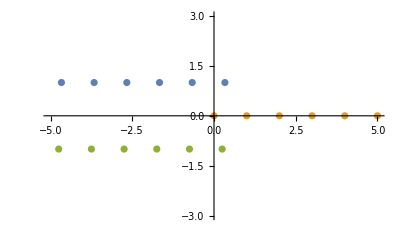

```mathematica
poles1={0,1,2,3,4,5};
poles2=-poles1+Complex[-a,1];
poles3=-poles1+Complex[-b,-1];
Magnify[ComplexListPlot[{poles2,poles1,poles3},PlotRange->{{-5,5},{-3,3}},GridLines->{{{1/8,Red}},{}},GridLinesStyle->Thick,PlotLegends->{MaTeX["\\Gamma(a+z)"],MaTeX["\\Gamma(-z)"],MaTeX["\\Gamma(b+z)"]}],1.5]
```

### Numerical results check

The numerical approximations given by the first 15 terms obtained with MBsums and MBConicHulls are compared. For MBConicHulls, both the straight and non-straight methods are tested on this example.
Since the example is simple, and only two series representations are obtained by MBConicHulls, we define a function that automatically chooses the converging series representation depending on the value of x (|x|<1 or |x|>1).
It is then possible to pick any value for x by replacing xval appropriately without having to worry about choosing the correct series representation each time a different value is chosen.

#### MBsums

```mathematica
MBsums[aval_,bval_,cval_,xval_,contour_]:=
Module[{time,res},
Block[{Print},
{time,res}=AbsoluteTiming[I1=MBint[Gamma[c]/(Gamma[a]Gamma[b])(-x)^z Gamma[-z]Gamma[a+z]Gamma[b+z]/(Gamma[c+z]),{{},{z->contour}}];
Lk={x->xval};
Sum1=MBIntToSum[I1,Lk,{z->R}];
N[DoAllMBSums[Sum1,15,Lk],16]]]]
```

#### MBConicHulls (non-straight contour)

```mathematica
MBCH[aval_,bval_,cval_,xval_,seriesList_]:=
Module[{time,res},
Block[{Print},
If[Abs[xval]<1,{time,res}=AbsoluteTiming[N[SumAllSeries[EvaluateSeries[ResolveMB[MBRep[Gamma[cval]/(Gamma[aval]Gamma[bval]),{z},{-x},{{-z,aval+z,bval+z},{cval+z}}]],{},seriesList[[1]]],{x->xval},15],16]],
{time,res}=AbsoluteTiming[N[SumAllSeries[EvaluateSeries[ResolveMB[MBRep[Gamma[cval]/(Gamma[aval]Gamma[bval]),{z},{-x},{{-z,aval+z,bval+z},{cval+z}}]],{},seriesList[[2]]],{x->xval},15],16]]]]]
```

#### MBConicHulls (straight contour)

```mathematica
MBCHStraight[aval_,bval_,cval_,xval_,contour_,seriesList_]:=Module[{time,res},Block[{Print},If[Abs[xval]<1,{time,res}=AbsoluteTiming[N[SumAllSeries[EvaluateSeries[ResolveMB[MBRep[Gamma[cval]/(Gamma[aval]Gamma[bval]),{z->contour},{-x},{{-z,aval+z,bval+z},{cval+z}}]],{},seriesList[[1]]],{x->xval},15],16]],
{time,res}=AbsoluteTiming[N[SumAllSeries[EvaluateSeries[ResolveMB[MBRep[Gamma[cval]/(Gamma[aval]Gamma[bval]),{z->contour},{-x},{{-z,aval+z,bval+z},{cval+z}}]],{},seriesList[[2]]],{x->xval},15],16]]]]]
```

#### Results

```mathematica
xval =1+2I; (*value of x considered*)
MBsums[a,b,c,xval,contour]
MBCHStraight[a,b,c,xval,contour,{2,1}]
```

{1.44518,-1.126153061236991-0.112543767882336 ⅈ}

{0.317376,-1.12615-0.112544 ⅈ}

The values obtained with the straight contour method (MBsums and MBConicHulls) agree.

```mathematica
MBCH[a,b,c,xval,{2,1}]
MBCH[a,b,c,xval,{1,2}]
```

{0.113091,-343.323-132.576 ⅈ}

{0.136268,1.05303+0.8645 ⅈ}

Since the poles were not separated, the non-straight contour do not enclose the same poles as the straight contour previously defined. The results are thus understandably different, and in this case wrong with respect to the integral defined.

### Performance comparison on a numerical check

We now repeat the same numerical calculations for a sample of 90 points chosen in both convergence regions (|x|<1 and |x|>1).

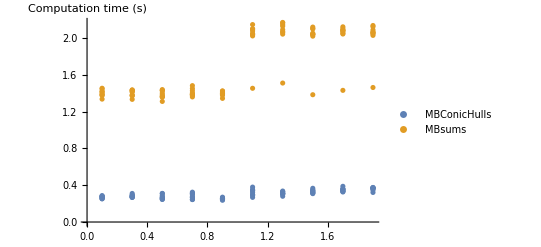

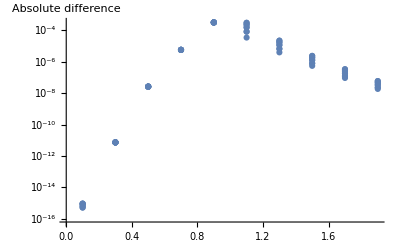

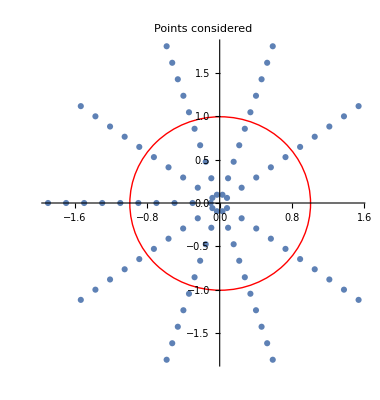

```mathematica
Clear[time1,res1,time2,res2]
data= {};
For[i=0,i<10,i++,
For[j=1,j<10,j++,
xval=(2i+1)/10Exp[I 2 j Pi/10];
{time1,res1}=MBCHContour[a,b,c,xval,contour,{2,1}];
{time2,res2}=MBsums[a,b,c,xval,contour];
AppendTo[data,{i,j,xval,time1,res1,time2,res2}]
]]
ListPlot[{Transpose@{Abs[data[[All,3]]],data[[All,4]]},Transpose@{Abs[data[[All,3]]],data[[All,6]]}},AxesLabel->{MaTeX["|x|"],"Computation time (s)"},PlotLegends->{"MBConicHulls","MBsums"}]
ListLogPlot[{Transpose@{Abs[data[[All,3]]],Abs[data[[All,5]]-data[[All,7]]]}},AxesLabel->{MaTeX["|x|"],"Absolute difference"}]
ComplexListPlot[data[[All,3]],AxesLabel->{MaTeX["\\Re(x)"],MaTeX["\\Im(x)"]},Epilog->{Red,Circle[{0,0},1],Thick},PlotLabel->"Points considered"]
```

## 2-Fold Integrals

### Parameters & test integral

```mathematica
MaTeX["I=\\frac{\\Gamma(c)}{\\Gamma(a)\\Gamma(b_1)\\Gamma(b_2)}\\iint_{i\\mathbb{R}\\times i\\mathbb{R}+\\delta}^{i\\mathbb{R}\\times i\\mathbb{R}+\\delta}\\frac{dz_1\\,dz_2}{(2i\\pi)^2}(-x)^{z_1}(-y)^ {z_2}\\Gamma(-z_1)\\Gamma(-z_2)\\frac{\\Gamma(a+z_1+z_2)\\Gamma(b_1+z_1)\\Gamma(b_2+z_2)}{\\Gamma(c+z_1+z_2)}, \\text{where}\\colon a=-\\frac{1}{3}, b_1=-\\frac{1}{4}, b_2=-\\frac{1}{5}, c=\\frac{1}{2},\\delta=-\\frac{1}{10}",Magnification->1.5]
```

-Graphics-

```mathematica
a=1/3;
b1=1/4;
b2=1/5;
c=1/2;
delta=-1/10;
```

### Numerical results check

```mathematica
xval=1/2+I/2; (*value of x considered*)
yval=1/2-I/2; (*value of y considered*)
```

#### MBsums

```mathematica
AbsoluteTiming[
int=MBint[Gamma[c]/(Gamma[a]Gamma[b1]Gamma[b2])(-x)^z1(-y)^z2 Gamma[-z1]Gamma[-z2](Gamma[a+z1+z2]Gamma[b1+z1]Gamma[b2+z2])/Gamma[c+z1+z2],{{},{z1->delta,z2->delta}}];
sum=MBIntToSum[int,{x->xval,y->yval},{z1->R,z2->R}];
N[DoAllMBSums[sum,30,{x->xval,y->yval}]]]
```

z1->R ( Re z1 > -1/10 )

z2->R ( Re z2 > -1/10 )

{1.76689,1.12045+0.0291898 ⅈ}

#### MBConicHulls

```mathematica
Block[{Print},AbsoluteTiming[
res=ResolveMB[MBRep[Gamma[c]/(Gamma[a]Gamma[b1]Gamma[b2]),{z1->delta,z2->delta},{-x,-y},{{-z1,-z2,a+z1+z2,b1+z1,b2+z2},{c+z1+z2}}]];
N[SumAllSeries[EvaluateSeries[res,{},1],{x->xval,y->yval},30],16]
]]
```

{0.509539,1.12045+0.0291898 ⅈ}

#### Built-in function AppellF1

```mathematica
N[AppellF1[a,b1,b2,c,xval,yval]]
```

1.12045+0.0291898 ⅈ

The values obtained with MBsums, MBConicHulls and the built-in AppellF1 function are identical, as expected.

### Performance comparison on a numerical check

We now repeat the same numerical calculations for a sample of 90 random points chosen in the first convergence region (|x|<1 ∧ |y|<1).

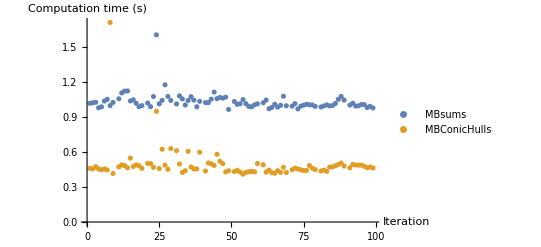

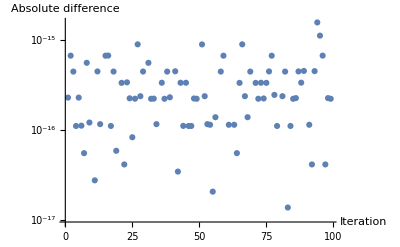

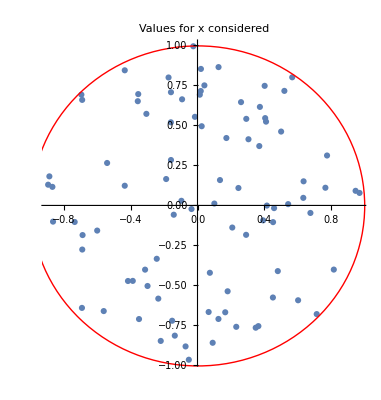

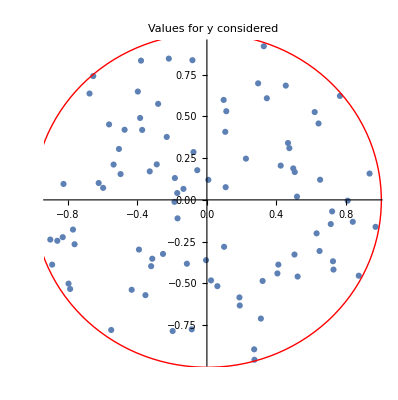

```mathematica
data= {};
For[i=0,i<10,i++,
For[j=1,j<10,j++,
While[xval=RandomComplex[{-1-I,1+I}];yval=RandomComplex[{-1-I,1+I}];Abs[xval]>1∨ Abs[yval]>1];
Block[{Print},
{time1,res1}=AbsoluteTiming[int=MBint[Gamma[c]/(Gamma[a]Gamma[b1]Gamma[b2])(-x)^z1(-y)^z2 Gamma[-z1]Gamma[-z2](Gamma[a+z1+z2]Gamma[b1+z1]Gamma[b2+z2])/Gamma[c+z1+z2],{{},{z1->delta,z2->delta}}];sum=MBIntToSum[int,{x->xval,y->yval},{z1->R,z2->R}];N[DoAllMBSums[sum,15,{x->xval,y->yval}]]];
{time2,res2}=AbsoluteTiming[res=ResolveMB[MBRep[Gamma[c]/(Gamma[a]Gamma[b1]Gamma[b2]),{z1->delta,z2->delta},{-x,-y},{{-z1,-z2,a+z1+z2,b1+z1,b2+z2},{c+z1+z2}}]];
N[SumAllSeries[EvaluateSeries[res,{},1],{x->xval,y->yval},15],16]
];
AppendTo[data,{i,j,xval,yval,time1,res1,time2,res2}]
]]]
ListPlot[{Transpose@{10data[[All,1]]+data[[All,2]],data[[All,5]]},Transpose@{10data[[All,1]]+data[[All,2]],data[[All,7]]}},AxesLabel->{"Iteration","Computation time (s)"},PlotLegends->{"MBsums","MBConicHulls"}]
ListLogPlot[{Transpose@{10data[[All,1]]+data[[All,2]],Abs[data[[All,6]]-data[[All,8]]]}},AxesLabel->{"Iteration","Absolute difference"}]
ComplexListPlot[data[[All,3]],AxesLabel->{MaTeX["\\Re(x)"],MaTeX["\\Im(x)"]},Epilog->{Red,Circle[{0,0},1],Thick},PlotLabel->"Values for x considered"]
ComplexListPlot[data[[All,4]],AxesLabel->{MaTeX["\\Re(y)"],MaTeX["\\Im(y)"]},Epilog->{Red,Circle[{0,0},1],Thick},PlotLabel->"Values for y considered"]
```